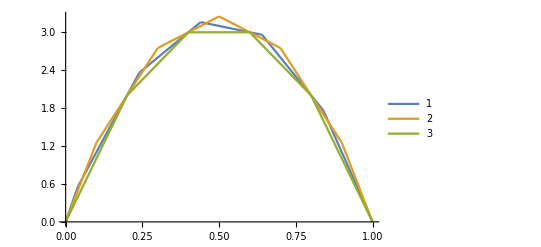

```mathematica
upperBound[alpha0_, m0_, p0_] :=Module[{alpha =alpha0,mPar=m0,p=p0},
hL[k_,m_,a_]:=k*(k+1)/2 - k*a;
hH[k_,m_,b_]:=(m-k)*(m-k+1)/2 - (m-k)*b;
omega[k_,m_,p_,a_]:=p*hH[k,m,1-a]+(1-p)*hL[k,m,a];
omegaMin[p_]:=Min[omega[#,mPar,p,alpha]& /@ Range[0,mPar]];
extremePoints = Table[
{(k+(1-alpha))/mPar, NumberForm[(k+(1-alpha))/mPar,2]},
{k, 0, mPar-1}
]~Join~{{0,0},{1,1}};
{omegaMin[p], extremePoints}
];
hh[p_]:=upperBound[1/2,5,p][[1]];
hd[p_]:=upperBound[1,5,p][[1]];
ha[p_]:=upperBound[5/6,5,p][[1]];
harb[alpha_,p_]:=upperBound[alpha,5,p][[1]];

Plot[
{harb[16/20,p],harb[1/2,p],harb[1,p]}, {p,0,1},
PlotLegends->Automatic,
PlotPoints->500
]
```

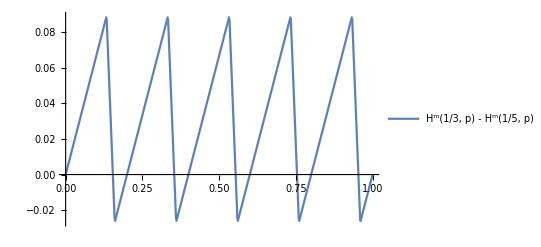

diffplot.eps

```mathematica
diffplot:=Plot[harb[1/3,p]-harb[1/5,p], {p,0,1},PlotLegends->{"H^5(1/3, p) - H^5(1/5, p)"}]
diffplot
Export["diffplot.eps",diffplot]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["diffplot.eps"]]]
```

```mathematica
Solve[harb[1/20,p]-harb[1/2,p]==0,p]
```

{{p→0},{p→2/11},{p→1/5},{p→21/55},{p→2/5},{p→32/55},{p→3/5},{p→43/55},{p→4/5},{p→54/55},{p→1}}

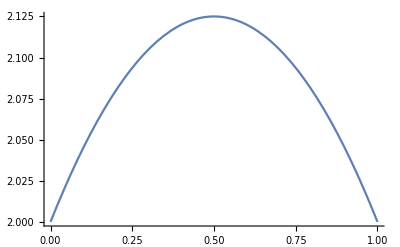

```mathematica
Plot[Integrate[harb[a,p],{p,0,1}],{a,0,1}]
```

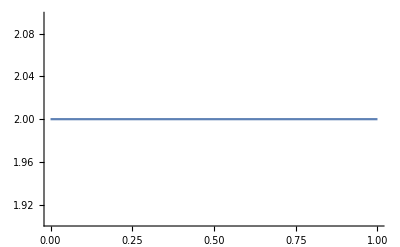

```mathematica
Plot[harb[b,4/5],{b,0,1}]
```